# Midterm 1

## Question 1

## 1.1

```mathematica
d[t_,a_,b_]:=(1+a*t)^(-b/a)
```

```mathematica
d[t,α,β]
```

(1+t α)^(-β/α)

```mathematica
d[t,α,β]
```

## 1.2

```mathematica
Log[d[2,α,β]]/Log[d[1,α,β]]
```

Log[(1+2 α)^(-β/α)]/Log[(1+α)^(-β/α)]

```mathematica
(-(b/a)*Log[(1+2 α)])/(-(b/a)*Log[(1+α)])
```

Log[1+2 α]/Log[1+α]

## Question 2

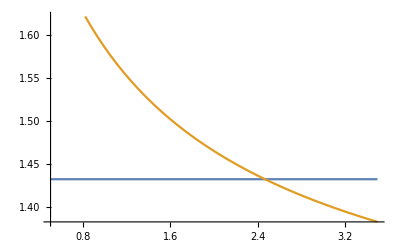

```mathematica
Plot[{Log[0.6]/Log[0.7],Log[1+2*a]/Log[1+a]},{a,0.5,3.5}]
```

```mathematica
FindRoot[Log[1+2*x]/Log[1+x]-Log[0.6]/Log[0.7],{x,2}]
```

{x→2.46797}

## Question 3

```mathematica
Exit[]
```

## 3.1

Suggested Answers:

```mathematica
Lagrangian1=Log[c0]+0.7*Log[c1]+0.6*Log[c2]-λ*(c0+c1+c2-K)
```

-((c0+c1+c2-K) λ)+Log[c0]+0.7 Log[c1]+0.6 Log[c2]

Or

```mathematica
budget=c0+c1+c2==K
objectivefunction =Log[c0]+0.7*Log[c1]+0.6*Log[c2] 
Lagrangian2=objectivefunction - λ*(budget[[1]]-budget[[2]])
```

c0+c1+c2==K

Log[c0]+0.7 Log[c1]+0.6 Log[c2]

-((c0+c1+c2-K) λ)+Log[c0]+0.7 Log[c1]+0.6 Log[c2]

Mathematica mark-up is not necessary but copying and pasting Mathematica code is OK.

Any notation is valid: log(c0), Log(c0), Log[c0], etc... No need to use λ for the multiplier. Using just l (letter l) or any other letter is fine, etc...

Remove 3 points for sign error  (+λ  instead of -λ) in the Lagrangian. But notice that there is no sign error in Log[c0]+0.7*Log[c1]+0.6*Log[c2]+λ*(K-c0-c1-c2).

Remove 7 points if an equality or inequality symbol appears in the Lagrangian: Log[c0]+0.7*Log[c1]+0.6*Log[c2]-λ*(c0+c1+c2==K)

As long as the objective function in the Lagrangian is correct award 3 points.

Blank item must receive zero grade

## 3.2

Suggested Answers:

```mathematica
Lagrangian1=Log[c0]+0.7*Log[c1]+0.6*Log[c2]-λ*(c0+c1+c2-K)
```

```mathematica
vars={c0,c1,c2,λ}
```

{c0,c1,c2,λ}

```mathematica
Solve[D[Lagrangian1,{vars}]==0,vars][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{c0→0.434783 K,c1→0.304348 K,c2→0.26087 K,λ→2.3/K}

## 3.3

Suggested answer: 2.3/K

If the Lagrangian was incorrect (due to sign error) and so the answer is -2.3/K award full points.

Answers different than 2.3/K and -2.3/K receive zero (I may regrade it later to award partial credit. This is just to save your time.

## 3.4

They are the same (by the Envelope Theorem). Computation in 3.3 may be wrong but if students state that they should be the same for theoretical reasons they should get full credit. All answers that ommitt that both answers should be the same should receive zero points.

## Question 4

```mathematica
f1={10,10,10000}
f2={0,30,10000}
f3={15,0,10000}
```

{10,10,10000}

{0,30,10000}

{15,0,10000}

```mathematica
h[u_,U_,θ_,δ_]:=((1-δ)*u^θ+δ*U^θ)^(1/θ)
```

## 4A1

```mathematica
U[2]=h[f1[[3]],0,1,0.5];
U[1]=h[f1[[2]],U[2],1,0.5];
U[0]=h[f1[[1]],U[1],1,0.5]
```

1257.5

## 4A2

```mathematica
U[2]=h[f2[[3]],0,1,0.5];
U[1]=h[f2[[2]],U[2],1,0.5];
U[0]=h[f2[[1]],U[1],1,0.5]
```

1257.5

## 4A3

```mathematica
U[2]=h[f3[[3]],0,1,0.5];
U[1]=h[f3[[2]],U[2],1,0.5];
U[0]=h[f3[[1]],U[1],1,0.5]
```

1257.5

## 4B1

```mathematica
U[2]=h[f1[[3]],0,0.1,0.5];
U[1]=h[f1[[2]],U[2],0.1,0.5];
U[0]=h[f1[[1]],U[1],0.1,0.5]
```

9.94094

## 4B2

```mathematica
U[2]=h[f2[[3]],0,0.1,0.5];
U[1]=h[f2[[2]],U[2],0.1,0.5];
U[0]=h[f2[[1]],U[1],0.1,0.5]
```

0.0169803

## 4B3

```mathematica
U[2]=h[f3[[3]],0,0.1,0.5];
U[1]=h[f3[[2]],U[2],0.1,0.5];
U[0]=h[f3[[1]],U[1],0.1,0.5]
```

0.733598

## 4C

Scenario B. One can see when θ=1 (scenario A), all flows are equivalent. But when θ=0.1 (scenario B), the first flow which is smoother (period 0 and period 1 utilities are the same) has a higher utility than the second flow (which has no utility in period zero but high utility in period 1) and the third flow (which has high utility in period zero but no utility in period 1).

## Question 5

## 5.1

```mathematica
L=f[x,y]-λ1*(-g1[x,y]-(-10))-λ2*(g2[x,y]-20)
```

f[x,y]-λ1 (10-g1[x,y])-λ2 (-20+g2[x,y])

## 5.2.1

(∂L)/(∂x)=0 and (∂L)/(∂y)= 0

## 5.2.2

```mathematica
λ1*(-g1[x,y]-(-10))==0
```

```mathematica
λ2*(g2[x,y]-20)==0
```

## 5.2.3

```mathematica
λ1>=0
λ2>=0
```

## 5.2.4

```mathematica
-g1[x,y]<=-10
g2[x,y]<=20
```